```mathematica
ShiftedSpacings//MatrixForm
```

(-4.99 | -3.99 | -2.99 | -1.99 | -0.99 | 0.01 | 1.01 | 2.01 | 3.01 | 4.01 | 5.01
-4.98 | -3.98 | -2.98 | -1.98 | -0.98 | 0.02 | 1.02 | 2.02 | 3.02 | 4.02 | 5.02
-4.99 | -3.99 | -2.99 | -1.99 | -0.99 | 0.01 | 1.01 | 2.01 | 3.01 | 4.01 | 5.01
-5.03 | -4.03 | -3.03 | -2.03 | -1.03 | -0.03 | 0.97 | 1.97 | 2.97 | 3.97 | 4.97
-5.01 | -4.01 | -3.01 | -2.01 | -1.01 | -0.01 | 0.99 | 1.99 | 2.99 | 3.99 | 4.99)

```mathematica
Table[testpt.i,{i,starvectors[[All,{1,2}]]}]
tmp=testpt.starvectors[[1,{1,2}]]
Table[x-tmp,{x,ShiftedSpacings[[1]]}]
```

{0.01,4.72404,4.01,-2.9258,-4.01}

0.01

{-5.,-4.,-3.,-2.,-1.,1.73472×10^-18,1.,2.,3.,4.,5.}

```mathematica
Position[ShiftedSpacings[[1]],_?(Chop[#-testpt.starvectors[[1,{1,2}]]]≥0&)]
```

{{6},{7},{8},{9},{10},{11}}

{{10,1},{2,5},{-1.86961,4.83435,0},2}

{-1.86961,4.83435,0}

{5,10,11,5,1}

{5,10,11,5,2}

{-1.86961,4.83435}

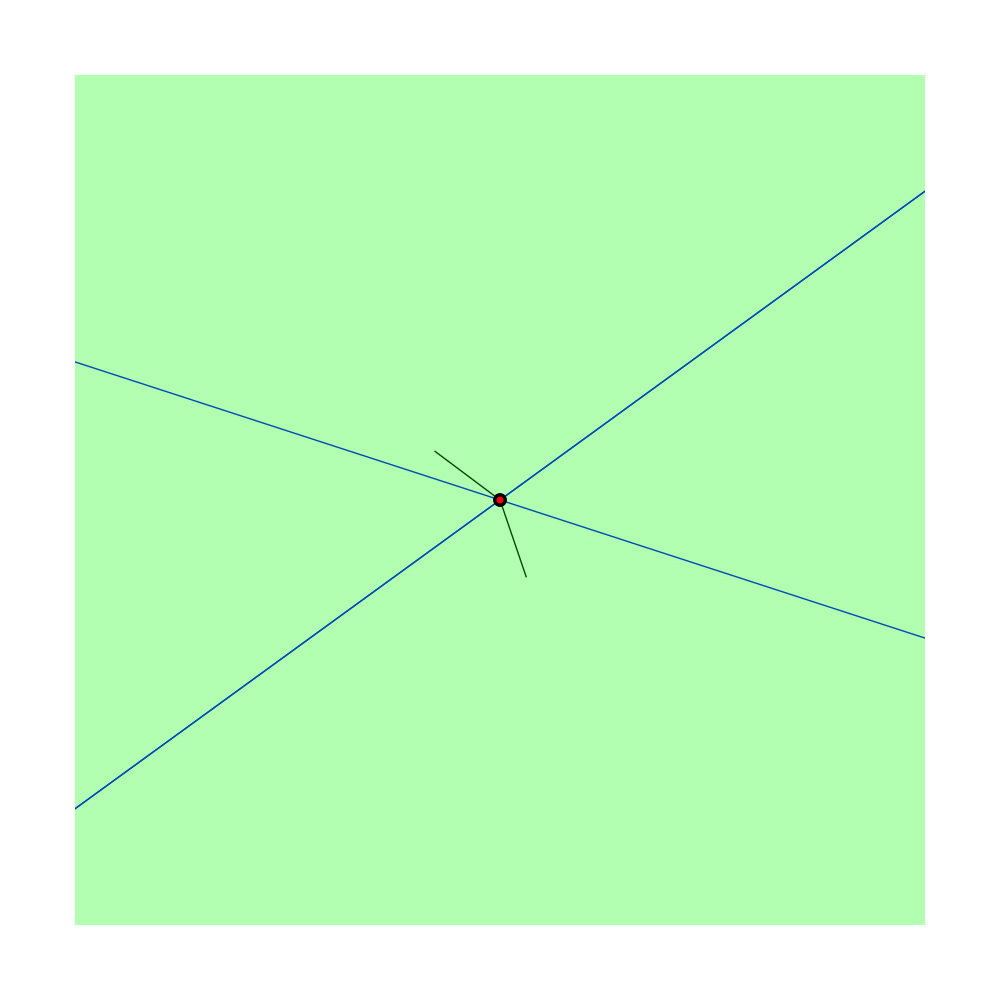

```mathematica
UniqueGridVertices[[633]]
testpt=UniqueGridVertices[[633,3]]
FindGridIndices[testpt]
FindGridIndices[Flatten[{ProbeVectors[[1]],0}]]

testpt=testpt[[{1,2}]]
eps=10^-3;
zoom=.005;
UpDown={-1,1};
ProbeIndices=Tuples[{UpDown,UpDown,UpDown,UpDown,UpDown}];
ProbeVectors=N[Table[testpt+eps*Normalize[n.starvectors][[{1,2}]],{n,ProbeIndices[[{2,5}]]}]];
ProbeVectorsArrow =Graphics[Line[{testpt,#}]&/@ProbeVectors];


Show[ProbeVectorsArrow,

Table[Plot[-starvectors[[i,1]]/starvectors[[i,2]]*x+ShiftedSpacings[[i,j]]/starvectors[[i,2]],{x,-maxlength,maxlength},PlotStyle->{Blue,Thin}],{i,Range[2,5]},{j,Range[numlines+1]}],
Table[Graphics[{Blue,Thin,Line[{{x,-maxlength},{x,maxlength}}]}],{x,ShiftedSpacings[[1]]}],


Graphics[{Green,Opacity[0.3],Polygon[{{-maxlength,-maxlength},{-maxlength,maxlength},{maxlength,maxlength},{maxlength,-maxlength},{-maxlength,-maxlength}}]}],
Graphics[{PointSize[0.01],Point[UniqueGridVertices[[All,3,{1,2}]]]}](*option here gets rid of indeterminate values*),
Graphics[{PointSize[0.005],Red,Point[testpt]}],
AspectRatio->1,PlotRange->{{testpt[[1]]-zoom,testpt[[1]]+zoom},{testpt[[2]]-zoom,testpt[[2]]+zoom}},
ImageSize->1000
]
```